{Ωcc 1/2+}

{3.73256,4.43726,{3.07251,2.93672,2.45379,2.04279}}

{0.470976}

{{0.325203},{0.308029},{0.860278}}

{Ωcc^* 3/2+}

{3.82755,4.63814,{3.07547,2.94482,2.46627,2.04279}}

{0.49058}

{{0.125455},{0.11883},{0.331875}}

{Ωbb 1/2+}

{10.44,3.71964,{3.05939,2.90169,2.40593,2.04279}}

{0.437783}

{{0.0261842},{0.0248014},{0.0692665}}

{Ωbb^* 3/2+}

{10.485,3.86405,{3.06241,2.90963,2.41599,2.04279}}

{0.454026}

{{-0.278072},{-0.263387},{-0.735599}}

{Ωccc 3/2+}

{4.85292,4.11798,{3.06723,2.92243,2.43314,2.04279}}

{0.665335}

{{0.546158},{0.517316},{1.44478}}

{Ωccb 1/2+}

{8.13223,3.59097,{3.0565,2.89418,2.39677,2.04279}}

{0.423487}

{{0.246823},{0.233788},{0.652935}}

{Ωccb^* 3/2+}

{8.15556,3.68605,{3.05865,2.89977,2.40356,2.04279}}

{0.433539}

{{0.324023},{0.306911},{0.857157}}

{Ωcbb 1/2+}

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{11.4073,2.9645,{3.03894,2.8502,2.34943,2.04279}}

{0.107409}

{{-0.0987535},{-0.0935384},{-0.261239}}

{Ωcbb^* 3/2+}

{11.4406,3.10933,{3.0436,2.86162,2.3608,2.04279}}

{0.110328}

{{0.107044},{0.101391},{0.28317}}

{Ωbbb 3/2+}

{14.6793,2.34242,{3.01265,2.78953,2.29743,2.04279}}

{0.25787}

{{-0.0943008},{-0.0893208},{-0.249459}}

{Mass Spectrum}

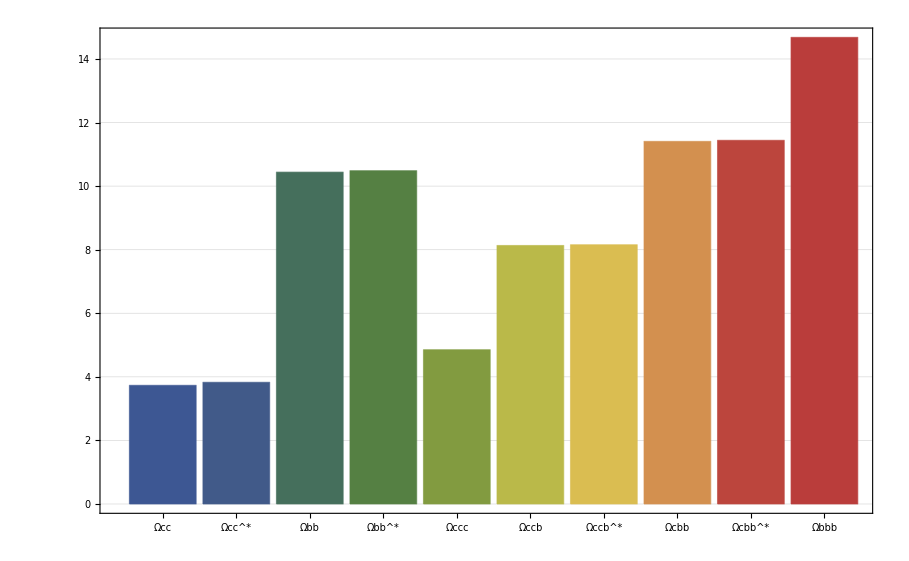

{Charge Radius}

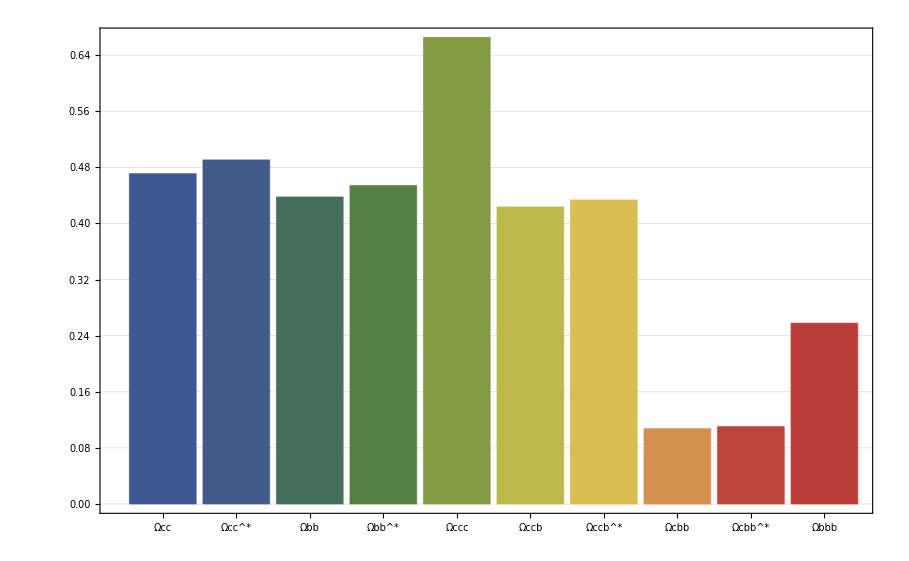

{Magnetic Moment}

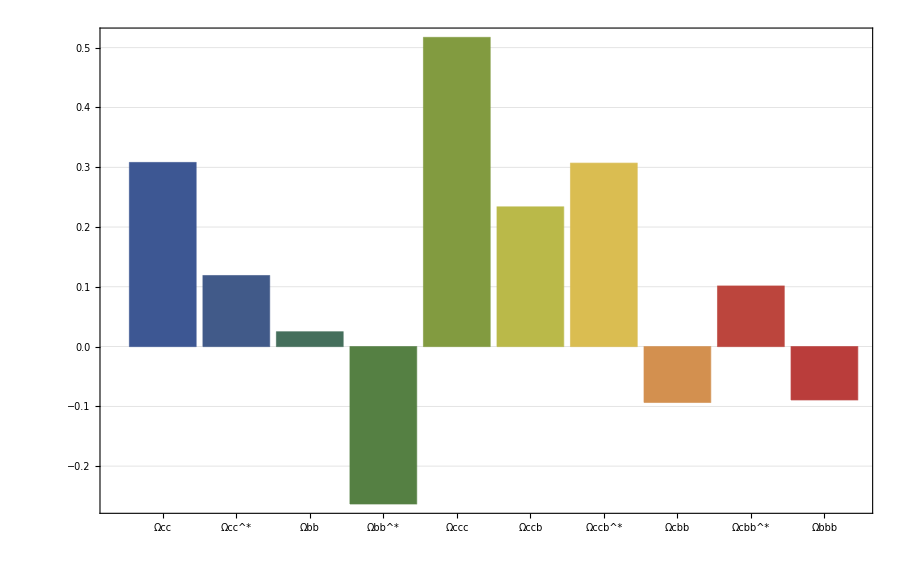

```mathematica
<<MITBagModel/MITBagModel.m

Nc=Hadron[{0,0,0,3},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,8}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}];
μNp=MagneticMoment[{0,0,0,4/3,-1/3},{0,0,0,0,0},Nc];
γμN=2.7928473446;

{"Ωcc 1/2+"}
Ωcc=Hadron[{0,2,1,0},{{0,0,0,0},{0,-8/3,32/3,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,-8/3,-16/3,0},{0,0,0,0},{0,0,0,0}}]
rΩcc=ChargeRadius[{0,2,1,0,0},{0,0,0,0,0},Ωcc];
μΩcc=MagneticMoment[{0,4/3,-1/3,0,0},{0,0,0,0,0},Ωcc];
{rΩcc}
{{μΩcc},{μΩcc/μNp},γμN{μΩcc/μNp}}

{"Ωcc^* 3/2+"}
ΩccStar=Hadron[{0,2,1,0},{{0,0,0,0},{0,-8/3,-16/3,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,-8/3,-16/3,0},{0,0,0,0},{0,0,0,0}}]
rΩccStar=ChargeRadius[{0,2,1,0,0},{0,0,0,0,0},ΩccStar];
μΩccStar=MagneticMoment[{0,2,1,0,0},{0,0,0,0,0},ΩccStar];
{rΩccStar}
{{μΩccStar},{μΩccStar/μNp},γμN{μΩccStar/μNp}}

{"Ωbb 1/2+"}
Ωbb=Hadron[{2,0,1,0},{{-8/3,0,32/3,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{-8/3,0,-16/3,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}]
rΩbb=ChargeRadius[{2,0,1,0,0},{0,0,0,0,0},Ωbb];
μΩbb=MagneticMoment[{4/3,0,-1/3,0,0},{0,0,0,0,0},Ωbb];
{rΩbb}
{{μΩbb},{μΩbb/μNp},γμN{μΩbb/μNp}}

{"Ωbb^* 3/2+"}
ΩbbStar=Hadron[{2,0,1,0},{{-8/3,0,-16/3,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{-8/3,0,-16/3,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}]
rΩbbStar=ChargeRadius[{2,0,1,0,0},{0,0,0,0,0},ΩbbStar];
μΩbbStar=MagneticMoment[{2,0,1,0,0},{0,0,0,0,0},ΩbbStar];
{rΩbbStar}
{{μΩbbStar},{μΩbbStar/μNp},γμN{μΩbbStar/μNp}}

{"Ωccc 3/2+"}
Ωccc=Hadron[{0,3,0,0},{{0,0,0,0},{0,-8,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,-8,0,0},{0,0,0,0},{0,0,0,0}}]
rΩccc=ChargeRadius[{0,3,0,0,0},{0,0,0,0,0},Ωccc];
μΩccc=MagneticMoment[{0,3,0,0,0},{0,0,0,0,0},Ωccc];
{rΩccc}
{{μΩccc},{μΩccc/μNp},γμN{μΩccc/μNp}}

{"Ωccb 1/2+"}
Ωccb=Hadron[{1,2,0,0},{{0,32/3,0,0},{0,-8/3,0,0},{0,0,0,0},{0,0,0,0}},{{0,-16/3,0,0},{0,-8/3,0,0},{0,0,0,0},{0,0,0,0}}]
rΩccb=ChargeRadius[{1,2,0,0,0},{0,0,0,0,0},Ωccb];
μΩccb=MagneticMoment[{-1/3,4/3,0,0,0},{0,0,0,0,0},Ωccb];
{rΩccb}
{{μΩccb},{μΩccb/μNp},γμN{μΩccb/μNp}}

{"Ωccb^* 3/2+"}
ΩccbStar=Hadron[{1,2,0,0},{{0,-16/3,0,0},{0,-8/3,0,0},{0,0,0,0},{0,0,0,0}},{{0,-16/3,0,0},{0,-8/3,0,0},{0,0,0,0},{0,0,0,0}}]
rΩccbStar=ChargeRadius[{1,2,0,0,0},{0,0,0,0,0},ΩccbStar];
μΩccbStar=MagneticMoment[{1,2,0,0,0},{0,0,0,0,0},ΩccbStar];
{rΩccbStar}
{{μΩccbStar},{μΩccbStar/μNp},γμN{μΩccbStar/μNp}}

{"Ωcbb 1/2+"}
Ωcbb=Hadron[{2,1,0,0},{{-8/3,32/3,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{-8/3,-16/3,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}]
rΩcbb=ChargeRadius[{2,1,0,0,0},{0,0,0,0,0},Ωcbb];
μΩcbb=MagneticMoment[{4/3,-1/3,0,0,0},{0,0,0,0,0},Ωcbb];
{rΩcbb}
{{μΩcbb},{μΩcbb/μNp},γμN{μΩcbb/μNp}}

{"Ωcbb^* 3/2+"}
ΩcbbStar=Hadron[{2,1,0,0},{{-8/3,-16/3,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{-8/3,-16/3,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}]
rΩcbbStar=ChargeRadius[{2,1,0,0,0},{0,0,0,0,0},ΩcbbStar];
μΩcbbStar=MagneticMoment[{2,1,0,0,0},{0,0,0,0,0},ΩcbbStar];
{rΩcbbStar}
{{μΩcbbStar},{μΩcbbStar/μNp},γμN{μΩcbbStar/μNp}}

{"Ωbbb 3/2+"}
Ωbbb=Hadron[{3,0,0,0},{{-8,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{-8,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}]
rΩbbb=ChargeRadius[{3,0,0,0,0},{0,0,0,0,0},Ωbbb];
μΩbbb=MagneticMoment[{3,0,0,0,0},{0,0,0,0,0},Ωbbb];
{rΩbbb}
{{μΩbbb},{μΩbbb/μNp},γμN{μΩbbb/μNp}}

{"Mass Spectrum"}
BarChart[{First[Ωcc],First[ΩccStar],First[Ωbb],First[ΩbbStar],First[Ωccc],First[Ωccb],First[ΩccbStar],First[Ωcbb],First[ΩcbbStar],First[Ωbbb]},Frame->True,ChartLabels->{"Ωcc","Ωcc^*","Ωbb","Ωbb^*","Ωccc","Ωccb","Ωccb^*","Ωcbb","Ωcbb^*","Ωbbb"},ChartStyle->"DarkRainbow",GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed]]

{"Charge Radius"}
BarChart[{rΩcc,rΩccStar,rΩbb,rΩbbStar,rΩccc,rΩccb,rΩccbStar,rΩcbb,rΩcbbStar,rΩbbb},Frame->True,ChartLabels->{"Ωcc","Ωcc^*","Ωbb","Ωbb^*","Ωccc","Ωccb","Ωccb^*","Ωcbb","Ωcbb^*","Ωbbb"},ChartStyle->"DarkRainbow",GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed]]

{"Magnetic Moment"}
BarChart[{μΩcc/μNp,μΩccStar/μNp,μΩbb/μNp,μΩbbStar/μNp,μΩccc/μNp,μΩccb/μNp,μΩccbStar/μNp,μΩcbb/μNp,μΩcbbStar/μNp,μΩbbb/μNp},Frame->True,ChartLabels->{"Ωcc","Ωcc^*","Ωbb","Ωbb^*","Ωccc","Ωccb","Ωccb^*","Ωcbb","Ωcbb^*","Ωbbb"},ChartStyle->"DarkRainbow",GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed]]
```